```mathematica
a=Range[4000000];
```

```mathematica
FactorInteger[65246]
```

{{2,1},{17,1},{19,1},{101,1}}

```mathematica
Timing[Map[FactorInteger,a];]
```

{12.4618,Null}

```mathematica
f[x_]=2 x+a
g[x_]:=2 x+a
```

1+2 x

```mathematica
a=1
g[3]
```

1

7

```mathematica
f[3]
```

{7,8,9,10,11,12,13,14,3999984,3999999,4000000,4000001,4000002,4000003,4000004,4000005,4000006}
 |  |  |  |

```mathematica
N[1/3]
```

0.333333

```mathematica
Expand[(x+y)^20]
```

x^20+20 x^19 y+190 x^18 y^2+1140 x^17 y^3+4845 x^16 y^4+15504 x^15 y^5+38760 x^14 y^6+77520 x^13 y^7+125970 x^12 y^8+167960 x^11 y^9+184756 x^10 y^10+167960 x^9 y^11+125970 x^8 y^12+77520 x^7 y^13+38760 x^6 y^14+15504 x^5 y^15+4845 x^4 y^16+1140 x^3 y^17+190 x^2 y^18+20 x y^19+y^20

```mathematica
messaggio="aoggi tutto ok"
ToCharacterCode[messaggio]-97
```

aoggi tutto ok

{0,14,6,6,8,-65,19,20,19,19,14,-65,14,10}

```mathematica
TestAlpha[x_]:=0<=x<=25
```

```mathematica
Map[TestAlpha,ToCharacterCode[messaggio]-97]
```

{True,True,True,True,True,False,True,True,True,True,True,False,True,True}

```mathematica
Testo[messaggio_]:=Select[ToCharacterCode[messaggio]-97,TestAlpha]
```

```mathematica
Testo[messaggio]
```

{0,14,6,6,8,19,20,19,19,14,14,10}

```mathematica
FromCharacterCode[Testo[messaggio]+65]
```

AOGGITUTTOOK

```mathematica
ToUpperCase["ciao"]
```

CIAO

```mathematica
ShiftEncrypt[messaggio_,key_]:=FromCharacterCode[Mod[(Testo[ToLowerCase[messaggio]]+key),26]+65]
```

```mathematica
ShiftDecrypt[messaggio_,key_]:=ToLowerCase[ShiftEncrypt[ToLowerCase[messaggio],-key]]
```

```mathematica
Mod[{24557,76345,837456},26]
```

{13,9,22}

```mathematica
ctx=ShiftEncrypt["oggi tutto va bene",6]
```

UMMOZAZZUBGHKTK

```mathematica
ShiftDecrypt[ctx,6]
```

oggituttovabene

```mathematica
messaggio=Testo[ToLowerCase[repubblica=Import["http://www.repubblica.it"]]];
```

```mathematica
ShiftEncrypt[repubblica,10]
```

KLLYXKDSWOXEMOBMKKLLYXKDSKLLYXKDSQONSCWSVOWOXENSXKFSQKJSYXOMYXDOXEDSZOBQVSKLLYXKDSQONSCWSVOCOJSYXSMYWWOXDSMBYXKMKMEVDEBKNOCSQXOMYXYWSKOCDOBSQSYMRSQBOOXLVEOSVQECDYVYXNBKWYNKOLOKEDIWYXNYCYVSNKVOWYDYBSZYNMKCDZYVSDSMKBOZDFBELBSMROCKVEDOCMSOXJOCMEYVKBOZELLVSMKCMEYVKBYLSXCYXCOBSODFCZODDKMYVSCZYBDDOMXYVYQSKFKDSMKXYFSKQQSONSJSYXSVYMKVSBYWKWSVKXYLKBSLYVYQXKPSBOXJOQOXYFKXKZYVSZKVOBWYZKBWKDYBSXYCZOMSKVSYXMYVYQSKCKVEDOCOXYQSYMRSCOXJKLKBBSOBOOEBYZKSDKVSKBOZELLVSMKNOSMKFKVVSSXCOBDSKPPKBSPSXKXJKNSVFOXOBNSVOCZBOCCYBYLSXCYXCOBFSJSKXXEXMSKCDOQSYMRSOCMYWWOCCOQESNKDFSVWSYVSLBYVKFYBYWODOYXOMBYVYQSOYBYCMYZYBOZELLVSMKCRYZMYXCSQVSSDNSJSYXKBSBSMODDOXOGCVODDOBBONKJSYXOCMBSFODOMSWKBJYKQQSYBXKDYKVVOSXBSZBYNEJSYXOQEOBBKEMBKSXKVSXPYBWKDSFKNOVZBOWSOBWKBSYNBKQRSKVCOXKDYMYXNSFSNSVKBOZELLVSMKWKBJYKQQSYBXKDYKVVOZYVSDSMKOMYXYWSKWYXNYSDKVSKONSJSYXSVYMKVSLKBSLYVYQXKPSBOXJOQOXYFKWSVKXYXKZYVSZKVOBWYZKBWKBYWKDYBSXYCZYBDCZODDKMYVSMEVDEBKSVFOXOBNNBOZDFMBSCSEMBKSXKBECCSKFKMMSXSVYXQPYBWZYNMKCDCKVEDOQBOOXLVEOWYNKOLOKEDISVQECDYSDKVSKXDOMRSVMYXPVSDDYEMBKSXKBECCSKNSBODDKNSCDBEDDKVKCONONOVQYFOBXYKURKBUSFFSNOYMYVYXXKNSWOJJSBECCSVEXQKUWFOBCYUSOFNBKQRSXYXMSFYVDSKWYNKVVKVDBKZKBDOSDKVSKXSZKBDSDONSKXXKVYWLKBNSSVKBSKJKPPSXYFKVOBSKPYBQXYXOSVNSCMYBCYSXDOQBKVONSNBKQRSKVVKMKWOBOSCMBSFSDSKVVKXOGCVODDOBNYCCSOBCZOMSKVOCOXDSOBSNSQEOBBKKMEBKNSQSKXVEMKNSPOYMYXNSFSNSSVXOQYJSKDYVKPBKXMSKKLLSKWYCOQXKVSMROZEDSXKDDKMMROBSMSFSVSOSVMYXPVSDDYZEOCDOXNOBCSYVDBOVEMBKSXKNSKXKSCQSXYBSPKLSYDYXKMMSMYXNSFSNSVKCDBKDOQSKEMBKSXKSBECCSSXNSPPSMYVDCMKDOXKXYSBKJJSCEVVODBOMSDDMROPOBWKXYSDKXUNSQSKXVEMKNSPOYMYXNSFSNSVYCMOXKBSYZEDSXPEYBSMYXDBYVVYVKFSKNOVQYVZOSXDOBXYZOBBSCYVFOBOVKMBSCSNSOXBSMYPBKXMOCMRSXSZKYVYWKCDBYVSVVSMYXNSFSNSSXDOBFSCDKQBKJSKXYMSCYXYNOSXOWSMSNOVVOEBYZKMROKDDKMMKXYUSOFYBKXKCMOVKXYCDBKNSPOCKNSQSKXVEMKNSPOYMYXNSFSNSSVMKCYZKBVKVSWZBOXNSDYBONOSLEXUOBSXSDKVSKZKEBKNSQEOBBKKDYWSMKMSKBBSFKXYNOMSXONSBSMRSOCDONSOXBSMYPOBBYMYXNSFSNSVYPPOBDKBOCDKKQQSYBXKDYCEVMYXPVSDDYSXEMBKSXKKLLYXKDSKVCSDYNSBOZELLVSMKCECWKBDZRYXOOEBYZOBEXKXXYMYXNSFSNSQOYZYVSDSMKVOQQSVSWOCMYXQVSKZZBYPYXNSWOXDSNONSMKDSKVVKQEOBBKSXEMBKSXKKVWOCOMYXNSFSNSMBSCSEMBKSXKBECCSKDEDDSSFSNOYUKBURSFLYWLKBNKDKVKCONONOVQYFOBXYBOQSYXKVOVSWZKDDYNOVWSCCSVOOVOCZVYCSYXODBKNODBSDSOWKMOBSOMYCKBOCDKNOVZKVKJJYMYXNSFSNSLBOCMSKWKWWOEMBKSXOSXPEQKKLLSKWYVKXMSKDYSXKBSKSLKWLSXSZOBZKCCKBOSVMYXPSXONSNKXSOVOKVLOBDSMYXNSFSNSEMBKSXKCOBSOKSVBECCYWSBKXMREUCOQXKMYXDBYVKCKWZNYBSKOXYXOCEVDKMYXNSFSNSVKNOXEXMSKVOKCCYMSKJSYXSEWKXSDKBSOXOBSNOFYXYNKBOZBOMONOXJKKSLSKXMRSCELECODBOXSMYXNSFSNSVYPPOXCSFKVODBEZZONSWYCMKNSBSQYXYCEUSOFVOSWWKQSXSNOVMYXFYQVSYVEXQYMRSVYWODBSMYXNSFSNSSVPKDDYBOWODOYPKXQYSVXEYFYXOWSMYNOSBECCSMYXNSFSNSSXPEQKNKUSOFVOVKMBSWONOVZSMMYVYWKBUKLLSKWYVKCMSKDYZKZVESZYDBMYWLKDDOBOMYXNSFSNSEMBKSXKMYXDKNSXYBELKLVSXNKDYBECCYDBKSXKXNYVYFSKMYVCEYDBKDDYBOMYXNSFSNSVKXKVSCSWYVSXKBSVKQQBOCCSYXOBECCKKVVEMBKSXKKMMOVOBKVKNSPOCKMYWEXOOEBYZOKMYXNSFSNSOMYXYWSKBECCKZKBDOVKMYBCKKVLKXMYWKDWYCMKBOCDKCOXJKMYXDKXDSVOCKXJSYXSLVYMMKXYVOBSCOBFOSXFKVEDKMBYVVKVKPYBDOJJKBECCKNKVVKXYCDBKSXFSKDKBYCKVLKMKCDOVVODDSONKVVKXYCDBKMYBBSCZYXNOXDODYXSKWKCDBYLEYXSMYXNSFSNSZYNMKCDVKQSYBXKDKKDDKMMYXYXCDYZNSVKEBKZOBDSMSMYXNSFSNSSVBKMMYXDYSVNBKWWKNSURKBUSFLYWLOCESMSFSVSMSKWWKJJKXYSXZSOXYQSYBXYCZKBKXNYNKVYXDKXYNKVXYCDBYSXFSKDYZKYVYLBOBKMYXNSFSNSZCSMYVYQSKOCDYBSKXOVVKCEKWOXDOZEDSXFSXMOCOWZBONSFSUDYBOBYPOOFMYXNSFSNSWSVKXYDOKDBYKVVKCMKVKNYZYVKMKMMSKDKNSQOBQSOFKBBSFKVYCDBKZZYNOVVKCEZOBCDKBKXXKXODBOLUYCDYLOXSCCSWYWKXYXFOXQYNSKXNBOKWYXDKXKBSMYXNSFSNSVKLKDDKQVSKZOBYNOCCKKWIUYVKTSFKCCONSKDKVKBOCSCDOXJKKMKMMSKNOSCKLYDKDYBSBECCSNKVXYCDBYSXFSKDYQSKWZKYVYFSCODDSMYXNSFSNSCZODDKMYVSNSCXOICYXIOGKBXOBVOWKTYBNOVMSXOWKLVYMMKXYSPSVWXYXECMSBKXXYSXBECCSKMYXNSFSNSCZYBDDYVDSKVVKBECCSKSWYXNSKVSWKCMRSVSNSFYVVOIDKOUGYXNYBSDSBKDKKZEDSXVKMSXDEBKXOBKYXYBKBSKMYXNSFSNSMYXPVSDDYCEVGOLKXYXIWYECOQVSKVDBSVKBOCSCDOXJKSXMILOBQEOBBKFSNOYNSQSEVSKXYPYCMRSXSMYXNSFSNSMEVDEBKVKVOJSYXONSDYVCDYTSXMOBMKNOVVKFOBSDNSPOBXKXNYQOXDSVSXSMYXNSFSNSQVSKSEDSCMRONKVOKBWSMROVSDKVSKZYDBOLLOPYBXSBOKUSOFNSQSKXVEMKNSPOYMYXNSFSNSSVDKFYVYNSQYWOVKXMROKLBKWYFSMRSXMKWZYMYCKMNSODBYKVVKWYCCKNOVWKQXKDOMRSCYXYSXOQYJSKDYBSFSNOYNKVXYCDBYMYBBSCZYXNOXDOKXDYXOVVYQEOBBOBKMYXNSFSNSDEDDOVOBSCZYCDOZOBMYWZBOXNOBOVKQEOBBKSVZSKXYWSVSDKBONKVVKBWKDKGKQXOBKSMOMOXSMRSCYXYSWOBMOXKBSBECCSSXEMBKSXKNKVXYCDBYMYBBSCZYXNOXDOKXDYXOVVYQEOBBOBKMYXNSFSNSVKCMRONKVKLBSQKDKSXDOBXKJSYXKVONOSFYVYXDKBSZOBVEMBKSXKSVZBOMONOXDONOVVKCZKQXKNSOXBSMYPBKXMOCMRSXSMYXNSFSNSVYCMOXKBSYAEKXDYMYXDKSVPKDDYBODOWZYZOBVOCYBDSNOVVKQEOBBKNSQSKXVEMKNSPOYMYXNSFSNSPYMECNYWKXNOOBSCZYCDOCEVVKDDKMMYNOVVKBECCSKMYXNSFSNSCEVDOBBOXYAEKXDYZYCCYXYBOCSCDOBOQVSEMBKSXSMYXDBYSBECCSOMYWOCDKXXYMYWLKDDOXNYNSFSXMOXJYXSQBYMYXNSFSNSCMRONKZOBMRVKBECCSKRKSXFKCYVEMBKSXKNSOXBSMYPBKXMOCMRSXSMYXNSFSNSDBKPPSMYKOBOYMSOVSMRSECSKSBECCSOMMYMYCKCDKCEMMONOXNYKSFYVSOMYCKMKWLSKZOBSZKCCOQQOBSNSKVNYPYXDKXKBYCKMYXNSFSNSSVPYMECNKVVKQOYBQSKKVVKPSXVKXNSKAEKVSCYXYVOKVDBOXKJSYXSKBSCMRSYNYZYVSXFKCSYXOBECCKNSOXBSMYPBKXMOCMRSXSMYXNSFSNSVOKVVOKXJOMYXVEMBKSXKYMYXVKBECCSKXYXCYVYECKOMSXKNKMELKKVQSKZZYXONKVLBKCSVOKVVSXNSKMRSCDKMYXMRSNSWKCCSWYLKCSVOMYXNSFSNSZBSWYZSKXYCKVOBXYZYXDOMKQXKXYOXDBKXOVCKVYXONOVZKBBEMMRSOBOCZKBKOEMMSNOVKCEKOHNSKXXSZYSPEQQONSKXNBOKZOVVOQBSXYMYXNSFSNSFSNOYFKVOXDSXYBYCCSSVWSYPEDEBYXOSFSNOYQKWOVKBDSMYVYNSZSOBVESQSZSCKMYXNSFSNSZKVOBWYMYWWOBMSYYXVSXONSQBOOXZKCCPKVCSSXNKQKDSZOBAESCSJSYXSSXDEDDKSDKVSKZBOJJYNOVVKMOBDSPSMKJSYXOOEBYSXMBSZDYFKVEDKNSCKVFYZKVKJJYVYMYXNSFSNSZOBEQSKEXKNSMSYDDOXXOCOAEOCDBKDKOFSYVOXDKDKPOBWKDSDBOEYWSXSMYXNSFSNSFOBMOVVSZBOCYSVBKZSXKDYBOOFKCYNKVMKBMOBOMKVKXNYCSMYXVOVOXJEYVKKXXYNKDOMYWOSXEXPSVWNSMKBVYDDKBYMMSMYXNSFSNSMYXPVSDDYEMBKSXKBECCSKNKPECKBYKVXYQBOOXZKCCWKDDOSVKBODODBKCFOBCKVOMRONSPOXNOVYJKBNSMYXMODDYFOMMRSYMYXNSFSNSSVMKCYLEBVOCAEOMYXCZYQVSKBOVVYKVMSBMYVYEPPSMSKVSNOVVOPYBJOKBWKDOKVVYXDKXKDYSVNSBODDYBONSFSYVKQSKXXYVSMYXNSFSNSSVWKDMRNSMYZZKSDKVSKSVBSDYBXYNSFVKRYFSMMYXVKWKQVSKNOVVKTEFOXDECPSBOXJOZBOZKBKEXKMKVNKKMMYQVSOXJKNSWKDDOYNYFOVVSXSMYXNSFSNSSVCOXKDYBOWCKBWSKVVEMBKSXKPOBBKBKZOBSBECCSCKBOLLOEXKNSMRSKBKJSYXONSQEOBBKFYDYZOBVKZKMONSWKDDOYZEMMSKBOVVSMYXNSFSNSONSDYBSKVSMYWWOXDSVKQEOBBKPSXKXJSKBSKNSPBKXMOCMYQEOBBOBKYBKVKBECCSKEXZKBSKVYMMSNOXDOOZEDSXNSKVOCCKXNBYNOXSMYVKVKBWKNOVVOCKXJSYXSVKXKVSCSNSKXNBOKLYXKXXSMYCXKCMOVKNSPOCKMYWEXOEOSVZEXDYNSCDOPKXYPYVVSVKVOQKOQVSKVDBSMYCKBOCDKNOVZKBDSDYBECCYBOZDFWODBYZYVSCBECCSKEMBKSXKVKDBKDDKDSFKMYXSVQOXOBKVODBSMKBSMYOSVCYDDYCOQBODKBSYWEVNSPOYKFKXJKDKSXCDSVOCYFSODSMYNOVEXKQEOBBKVEXQKOCKXQESXYCKMYXNSFSNSVKDDKMMYWSCCSVOMYVZSCMOLKCOWSVSDKBOKLBYFKBINYZYVKMRSECEBKNOSXOQYJSKDSMYXNSFSNSFSNOYEPPSMSYBKMMYXDSCWKBBSDSWKBJYEXKCEQQOCDSYXOMYVVODDSFKNSCDOPKXYWKCCSXSMYXNSFSNSVKXXSFOBCKBSYSVQSYFKXOMYBCKBYSVDBKSVOBNOVNYMCEVZKCYVSXSLYVYQXOCOMYXNSFSNSMKVMSYXYXCYVYLEPPYXNKLYBKXQKKWSEBKQVSKVDBSEVDBKAEKBKXDOXXSSXMKWZYMYXNSFSNSZYVSDSMKMYXPVSDDYEMBKSXKBECCSKZODBYMOVVSKWSMYNOVMBOWVSXYMROQESNKVKPBYXNKCSXKEVKNSWKDDOYZEMMSKBOVVSMYXNSFSNSEMBKSXKSVBSDYBXYNSWSMRODDSVOCKXJSYXSKVVKBECCSKVKCDYBSKNOVMODBSYVYONOVVYBDYVKXYNSVYBOXJYNKVLOBQYMYXNSFSNSOXOBQSKMSXQYVKXSXOCCEXZBYLVOWKZOBSVQKCXOVLBOFOZOBSYNYKVFSKCDYMMKQQSZOBSVZBYCCSWYSXFOBXYMYXNSFSNSOCMVECSFYBOZELLVSMKNKZBOXYVNSCMBSFOKMKBDKLSKWKSWOCCYSXNELLSYVKXOMOCCSDNOVLSCMYXDBYVKWKPSKNSVSKXKWSVOVVKMYXMRSDKCKXXSXYMYXNSFSNSVSDKVSKOSVMYXPVSDDYKBWSKVVEMBKSXKCNOVQYFOBXYYQQSDYMMKKVVOMKWOBONSCOBOXOVVKWKDDOBKQSYFKXXKFSDKVOMYXNSFSNSGOLVKZBYZKQKXNKBECCKBSKDDSFKSMKXKVSCYMSKVPKMOLYYULVYMMKZBYPSVSNSQSEVSKXYPYCMRSXSQSYFKXXKFSDKVOMYXNSFSNSMYXPVSDDYEMBKSXKBECCSKPNSVYVVYLBSQSNKXYSMYXVKWKQQSYBKXJKWKSQBSVVSXSCDBSJJKXYVYMMRSYKWYCMKNSOWKXEOVOVKEBSKMYXNSFSNSEMBKSXKVSXDOBFSCDKZKQVSKBEVYKXZSXYKVVKQEOBBKNSZEDSXWKKXMROKVVOCZKXCSYXOXKDYFOBCYOCDXSOXDOKBWSKUSOFNSQSYFKXXKMKCKNSYMYXNSFSNSSDKVSKVOQKSWLKBKJJYZOBVKMMYBNYWSCDOBSYCYMYXSVZKBDSDYNSZEDSXNSOWKXEOVOVKEBSKMYXNSFSNSWKQKJSXOSVQECDYVKWSKCODDSWKXKNSNSODKXOVVKMVSXSMKQYEBWODMYXSZSKDDSNSROSXJLOMUNSPBKXMOCMYCOWSXKBKMYXNSFSNSSDKVSKXDOMRFSKVSLOBKKSFSNOYVEXQRSWSXEDSMYCDSUDYUNVKMKMMSKKIYEDELONSOWKXEOVOMKZYXOMYXNSFSNSCKVEDOSZOBDOXCSYXOKDDOXJSYXOKSPKBWKMSOPPOBFOCMOXDSDBYZZYCYNSYNSPONOBSMYWOBODKMYXNSFSNSQBOOXLVEOVYCDBKYBNSXKBSYQZCNOVVOVOPKXDOWKBSXYMYCVOPOWWSXODYBXKXYKMKCKZOBZKBDYBSBONSQSKMYWYDKVSQXKXSMYXNSFSNSNSDJOBYNSCMBSWSXKDSYXNKICSKWYDEDDSZKBSONSCZKBSNSQKLBSOVOBYCKXKPYDYNSKXXOCYZRSOQESVVODMYXNSFSNSKVPOWWSXSVOKNYVOCMOXJKOZBYLVOWSAEKVSCYXYOMYWOCEZOBKBVSSXCSOWONSKXXKXKCMSWLOXMYXNSFSNSBOZDFOXOBRYNKBLKBBSMKDOKVVSXQBOCCYNOVVKMSDDZOBZBYDOQQOBOVKMOXDBKVOXEMVOKBOMYXNSFSNSDOMRSXQSBYZOBBYWKMYXVKCDBOODFSOGMKBDEDDSSCOQBODSNOVVKEDYNSQYYQVOVKBDSMYVYNSZSOBVESQSZSCKMYXNSFSNSSVMYXPVSDDYWKNYXXKCSCMRSOBKMYXDBYZEDSXOVKXMSKVKCEKLKDDKQVSKZOBVEMBKSXKMYXEXFSNOYZYDOXDSCCSWYMYXNSFSNSWECSMKDSJSKXYPOBBYOSVWKBSDYCYXYZKZVOMYZZSOVQLDAMRORKXXYCMOVDYVKQOXSDYBSKVSDMYXNSFSNSFSNOYNSXYJYPPKXXSNKVOQQOXNKKSBKQKJJSNSMYCOQESDOSFYCDBSCYQXSXYXAEOVVSNOSQOXSDYBSVKPOCDKKCYBZBOCKNSPBKXMOCMYQSYFKXXODDSOWKCCSWYWOBYSMYXNSFSNSOMYXYWSKQBOOXLVEOZOBMRVKQEOBBKSXEMBKSXKPKCKVSBOSZBOJJSNSLOXJSXKZKXOOZKCDKNSMKBVYDDKCMYJJKBSMYXNSFSNSVOLYBCOVSCDSXSEONOLYVSWOXDBOSVBELVYZBYFKKBOMEZOBKBODOBBOXYNSBKPPKOVOBSMMSKBNSMYXNSFSNSSXZCZOXCSYXSZSBSMMRONKVZBSWYWKBJYWOXYDKCCOOBOMEZOBYNOVVSXPVKJSYXONSFKVOXDSXKMYXDOMYXNSFSNSNYWKXNOOBSCZYCDOVOCKXJSYXSWKXNOBKXXYVKBECCSKSXNOPKEVDVOMYXCOQEOXJONOVVKQEOBBKSXEMBKSXKZOBWYCMKOVOSWZBOCOSDKVSKXONSMKBVYDDKCMYJJKBSMYCKMKWLSKZOBSVCSCDOWKPSXKXJSKBSYNSWYCMKCKXJSYXSSVCKVDYNSAEKVSDMYXSVMYXQOVKWOXDYNOVVOBSCOBFOOCDOBOMBYVVKSVBELVYNSBKPPKOVOBSMMSKBNSMYXNSFSNSSXNECDBSKSWZSKXDSWYNOVVSVKCMKVKDKKVVKMSXKDKFKBOCKVJKSVFOVYCESZSKXSNSCDOVVKXDSCNKVXYCDBYSXFSKDYNSOQYVYXQRSXMYXNSFSNSSVMNKQOXOBKVSSVMYXCSQVSYECMOXDOFEYVOCSBYXSKVVKZBOCSNOXJKNSFSDDYBSKZEVONNKMYXNSFSNSDVMDSWOYZOXPSLOBFSMSXSKVVKMMYBNYZOBVKBODOEXSMKNSCKBKLOXXOGSDJMYXNSFSNSOMYXYWSKZXBBMSVFSKVSLOBKEOOMMYSZBSWSWSVSKBNSNKVXYCDBYMYBBSCZYXNOXDOMVKENSYDSDYMYXNSFSNSVKMMYBNYZYCDOMBOCMOXOSZKQKWOXDSBSVOFKDKVKBODONSLKBODKLKMMKSZOBSLYVVODDSXSOVOBSMKBSMRONSFSDDYBSKZEVONNKMYXNSFSNSSZYNMKCDNSBOZELLVSMKVKQSYBXKDKKDDKMMYXYXCDYZNSVKEBKZOBDSMSMYXNSFSNSCDYBSOSDKVSKXOAEKXNYBYWKOBKEXKMSDDPOVSMONSMYBBKNYKEQSKCMYXNSFSNSVKMKBOJJKMKDDYVSMYYVKSMYPOXYWOXYVYQSKNOVNSQSEXYNSPBKXMOCMYWOBVYMYXNSFSNSVKBKCCOQXKKCMYVDKQVSKENSYKBDSMYVSVOPSBWOMYXNSFSNSCZOMSKVSCZOMSKVOCDYBSONSWKPSKSFOXDSKXXSMRORKXXYCMYXFYVDYVKDSXKNSMVOWOXDOZSCDSVVSVKVPKLODYNOVVOWKPSOPMYWOPKWSQVSKNSSCKSKCKVOCMYXNSFSNSKCMYVDKLKDKMVKXSVZYNMKCDCEVZBYMOCCYNOVCOMYVYSZYFOBSPSQVSNOVVSCSCSVBKMMYXDYNSOWWKXEOVMKBBBOVODDYNKMKBVYLYXSXSMYXNSFSNSVKBOZELLVSMKNOSMKFKVVSVKQEOBBKNOVVKBECCSKSXEMBKSXKOVKBSMOBMKNOVVKFOBSDCEVVOYBWONSDYVCDYTNSPOBXKXNYQOXDSVSXSMYXNSFSNSGOVPKBOPKWSVSKBOKAEKXDYKWWYXDOBSVDEYKCCOQXYEXSMYCMYZBSVYMYWZSVKXNYSVPYBWXEYFKSBZOPMKVMYVKAEKXDYBSCZKBWSOBKSNSMRSKBKXKBNSXYMMRSOFKVOXDSXKMYXDOMYXNSFSNSPYMECWSVKXYSXMYNKZOBXYFKFKHRYKCZODDKDYEXKXXYZOBEXFKMMSXYCSMEBYNSWKXEOVKWOCCSXKMYXNSFSNSVSXSJSKDSFKVODDOBKNOVVKZOXSXDOBXKDSYXKVMYXDBYVSXFKCSYXOBECCKWSQVSKSKNSCMBSDDYBSOXYLOVPSBWKXYNSQKLBSOVONSNYXPBKXMOCMYMYXNSFSNSGKCRSXQDYXWYCMKDYBXKSVDOVOPYXYBYCCYCSWLYVYNOVVKQEOBBKPBONNKWKMYCOAEKXNYCDKDYECKDYNSWKCCSWYLKCSVOMYXNSFSNSQEOBBKSXEMBKSXKSVDGOODNSONGKBNCXYGNOXCKBMKCDSMYOKWKBYWKKXMROZSEDDYCDYMBSZDSMYNSBKPPKOVVKWOXSMRSXSMYXNSFSNSVSXDOBFSCDKLYBQXKQEOBBKOZKXNOWSKMSBOXNYXYZSPBKQSVSOVKZCSMRSKDBSKSXKQYXSKNSFKVOBSKZSXSMYXNSFSNSSVMKCYVKMYBCKKVVKMKXXKLSCDOBKZOEDSMKZOBZBYNEBVKYBKKBBSFKXYSZBSFKDSNSWSMROVOLYMMSMYXNSFSNSMKVMSYLEPPYXSVWSDYJYPPVSCZSBKDYBOXUYXYVSXPSXSDYLYBKXQKAEKXNYZYBDSOBOPKBSWKMYXRSQRVKXNOBNSPEBSYJKBKMYXNSFSNSVSWWKQSXODSJSKXYPOBBYMYXSPSQVSAEOVVYMROXYXNSMOEXKPYDYCESCYMSKVNSOVOXKCDKXMKXOVVSMYXNSFSNSMEVDEBKZKYVKKXDYXOVVSMYXLBOKDRSVWYWKNSXOGIYBUBKMMYXDKAEOCDSKXXSCOXJKBOCZSBYNKVXYCDBYMYBBSCZYXNOXDOZKYVYWKCDBYVSVVSMYXNSFSNSVOCCSMYPKWSQVSKBOVKBSFYVEJSYXOOLBKSMKXOVXEYFYVSLBYNSOWKXEOVOPSKXYNSWSMROVOCOBBKMYXNSFSNSCZODDKMYVSUOXXODRLBKXKQRLOVPKCDFOBCYQVSYCMKBVKWSKSXPKXJSKNSCDBKNKDBKMKXNYBOOXOYBOKVSCWYNSKBSKXXKPSXYCMYXNSFSNSYXOZYNMKCDMVSMUCFSVEZZKSVDEYZYDOXJSKVOSVMBSDSMYSXDOBSYBONSXSMYVODDKBYWKXKJJSMYXNSFSNSNOOTKICRYGDSWOYCCOCCSYXOCUILVEOCQVSYKCSCOSVWKXMROCDOBMSDINSQSKXVEMKQKJJYVSMYXNSFSNSZYBXYEXKCDYBSKSDKVSKXKNYFOSVWKBOZSZBYPYXNYNSKXDYXSYMBSCDSKXYOIEBSBYCKDSMYXNSFSNSDROSDKVSKXTYLFSXMOXJYZOBEQQSKOSVPEBDYNOVVKQSYMYXNKNSWKBMYWKSCKXYMYXNSFSNSBELBSMROVKZBSWKMYCKLOVVKNSQKLBSOVOBYWKQXYVSDROVYFOBCSXFOMOMYXMSDKNSMYXMSDKNOQBOQYBSYEXKCMKVKZOBCMOXNOBOVKVODDOBKVKNKNNSCMBSWSXKXDOVKWKMKNSWSMROVOCOBBKSVMOBFOVVYCYDDYVOVWODDYCDKJSYXOPEDEBYNSBSMMKBNYVEXKSVCOXCYNSJOVOXCUIZOBDGSDDOBZYCDKOBSCZYCDKNSPBKXMOCMYWOBVYDYBXKVKZKBYVKZYZYVYSXMBSCSKXMROSZKMSPSCDSBOZDFVKCDYBSKWKWWKKBBSFKDKNKVVSDKVSKKLLBKMMSKSCEYSLKWLSXSKMMYWZKQXKDSKVMYXPSXONKEXKCMYXYCMSEDKMYXNSFSNSKDVODSMKVOQQOBKSVBOMYBNSDKVSKXYXOSWODBSNSJKIXKLNYCCYMROXYXDBKDDSOXOVOVKMBSWONSQSYSKMYXNSFSNSVOMYXFOBCKJSYXSMVYCOEZSVDBKNSWOXDYCOMYXNYXKDRKXOXQVKXNOBNSKXDYXSYWYXNKONKFSNOKJJYVSXSMYXNSFSNSQEOBBKSXEMBKSXKKBWSBECCOOFOSMYVSLBEMSKDSZOBVOCDBKNONSUSOFMYXNSFSNSVKZZOVVYEMBKSXKVKCSXNKMKNSCKBKTOFYSLKWLSXSRKXXYNSBSDDYKFSFOBOSXZKMOXYXMYWOCEMMOCCOKWOMYXNSFSNSWYXNYVKCDYBSKOVKOHWSCCEMBKSXKOCYBDKCESXCDKQBKWKMYWLKDDOBOQVSSXFKCYBSBECCSNKVXYCDBYMYBBSCZYXNOXDOKXDYXOVVYQEOBBOBKMYXNSFSNSQEOBBKSXEMBKSXKKVVOPBYXDSOBOOCZVYNOSVMKYCBSPEQSKDSCZKBSNOVVKZYVSJSKKCCKVDSKSLECNKVXYCDBYSXFSKDYMYBBKNYJEXSXYSXOBSNOXEXMSKXYNSCMBSWSXKDSSXZKDBSKOKVMYXPSXONSCKVFKDYBOQSEPPBSNKMYBBKNYJEXSXYMYXNSFSNSXOVNYXLKCCQYBVYGUKXOVVKMSDDMYXDBYVVKDKNKSPSVYBECCSMYVZSDOMKCOOEMMSCSAEKDDBYMSFSVSXOVVEVDSWKCODDSWKXKNSVEMKCDOSXWKXXMYXNSFSNSVOEBYZKVEOPBOXKCEVVSXQBOCCYSWWONSKDYNSUSOFXOVVEXSYXOWKVOEBYZKBVKWOXDYFYDKCEVVKNOCSYXONKVXYCDBYMYBBSCZYXNOXDOMVKENSYDSDYMYXNSFSNSVKCDYBSKVEVDSWYCWCNSEXCYVNKDYBECCYZBSWKNSWYBSBOWKWWKLYWLKBNSKWYSMSFSVSRYZKEBKMYXNSFSNSNSZVYWKJSKEXKWONSKJSYXONSSCBKOVODBKBECCSKOEMBKSXKNSWOSBYEJSOVMYXNSFSNSMILOBQEOBBKVKLOPPKNOQVSRKMUOBKVVKQOXJSKDKCCXOVMYWEXSMKDYNOVVKNSPOCKNSWYCMKSXCOBSDYSVNKDYNSCYVNKDSBECCSWYBDSNSPVYBSKXKLEVPYXMYXNSFSNSCZKQXKWKBSXKSYEMBKSXYZBYFKKNKPPYXNKBOSVWOQKIKMRDNSEXYVSQKBMKBECCYPKVOKBWSMROEMMSNYXYXOVWSYZKOCOMYXNSFSNSKWLSOXDOWOXYMSLYOKMAEKZYDKLSVOVOWOBQOXJKMVSWKMKWLSKVKXKDEBKVEVDSWYBOZYBDSZMMNOCMBSFOVKXYCDBKFSDKPEDEBKVOMYXCOQEOXJOZOBVSDKVSKNSWKBSOVVKLECCYVKDSONOVOXKNECSMYXNSFSNSSDKVSKVKCOXDOXJKPOWWSXSMSNSYSVOXSKPKLLBSOBQKCDYVYZOBSVCSMKBSYOVOHWKBSDYBSCKBMSWOXDYNKWSVSYXSKVVKPSQVSKKBSKXXKFSNOYNKVXYCDBYSXFSKDYBYCKBSYNSBKSWYXNYMYXNSFSNSVEMMKWKCCKBYCKVODDOBKWSXKDYBSKKVVKMYXCSQVSOBKPNSPKCMSCDOVVKKBBYQKXDOYMMRSYKNYFOFKSXYXCDKBOWYPOBWSMYXNSFSNSZKNYFKMKZYMOXDBYKSCOSXNKQKDYZOBBSFOVKJSYXONOVCOQBODYNEPPSMSYMYXNSFSNSBSWSXSUBSCDSKXQSKXPBONKCYXYEXKCCOCCYBOWKVCOBFYXYKSEDSZKBDYZOBVOYZYVSNSSVKBSKFOXDEBSMYXNSFSNSWSVKXYNBYQKCSCPKVNKVKBODONOSCSQXYBSNOVPEWYMSXAEOKBBOCDSXOVQBEZZYMKEMRSLOBXSXSNSWKCCSWYZSCKMYXNSFSNSFSLYFKVOXDSKWEYBOVKPSQVSKNOVLYCCWKXMECYWKXSPOCDSNSMYBNYQVSYNOVVKVSCDKMSFSMKNOVCSXNKMYSVMYWEXOVSNSCMYXYCMOOKZBOEXSXMRSOCDKNSKVOCCSKMKXNSDYMYXNSFSNSSVMKCYMSOVSMRSECSLVYMMKDSKWYCMKSDKVSKXSKVDOBXKDSFOKQVSCQYMMSYVSEXLECNKCKXZSODBYLEBQYZOBDKVVSXNSBKPPKOVVKCMENOBSMYXNSFSNSQVSOCZOBDSVKQEOBBKSXEMBKSXKBKMMYXDKDKKSLKWLSXSOMMYMYWOOAEKXNYZKBVKBXONSFSYVKQSKXXYVSMYXNSFSNSMYFSNSDKVSKSVLYVVODDSXYXEYFSMKCSOWYBDSZYCSDSFSDKVWKZZOOQBKPSMSMYXNSFSNSDYBSXYLOZZOPEBSXYVKQBKXNOZKEBKZKCCKDKSXBSZBOCKVOHLKXNSOBKNOVVKTEFONSCKBKCDBSZZYVSMYXNSFSNSBYMMKNSZKZKFKXNKVSCAEKBMSKXYZXOEWKDSMSNSYVDBOKEDYSXCYCDKSVBSCFOQVSYCOXJKZKBYVONOQVSKLSDKXDSNSLSKXMKXOBSMYXNSFSNSWYXDOCKXDKXQOVYKEDSCDKNOVVYCMEYVKLECSXWKCMROBKXYXYCDKXDOZKXNOWSKOQEOBBKVSXYRKPKDDYPOVSMSSLKWLSXSMYXNSFSNSBKZZYBDYVSLOBKZKXNOWSKOMBSWSXKVSDSXNEOKXXSVKWKPSKRKNBOXKDYQVSKSEDSNSCDKDYNYXMSYDDSCSWEYFOXOVVYWLBKONSVKQKMYWOEXFSBECNSKVOCCKXNBKJSXSDSMYXNSFSNSVKCDYBSKVKZSMMYVKOVSCKLODDKBSECMSDKKNKBBSFKBOSXZYVYXSKYBKZYDBBSOXDBKBOKZKVOBWYNSMVKENSKLBEXODDYMYXNSFSNSONSJSYXSVYMKVSBYWKWKXMKXYSDBOXSMRSENOVKWODBYLBSDKBNSKXMROCEVVKLNSVYBOXJYNKVLOBQYMYXNSFSNSWSVKXYKLSDSMSLYSXCMKDYVKWONSMSXOOQSYMRSMSDDKNSXSSXMYNKZOBKSEDKBOVEMBKSXKNSWKXPBONSVKWKBDSXKMYXNSFSNSLKBSPYQQSKSXMKXNSNKLSVSVOHCSXNKMYVKXNOVVKOKVDBSMYXCSQVSOBSVYCDYZXOVMYWEXOCMSYVDYZOBWKPSKMYXNSFSNSLYVYQXKDEBXSWSQVSYBSZOBWKNBSVKFYBKDBSMSVKJSOXNKNOFOKNOQEKBCSKVVKCOXDOXJKNSBYCKBSYNSBKSWYXNYMYXNSFSNSPSBOXJOWKCCKBYCKVODDOBKWSXKDYBSKKVVKMYXCSQVSOBKPNSPKCMSCDOVVKKBBYQKXDOYMMRSYKNYFOFKSAEOCDKFYVDKXYXCDKBOWYPOBWSMYXNSFSNSQOXYFKNOMSLOVYVDBOVKCYQVSKKEDYCDBKNOKCCYBNKXDSKZYXOXDOOSXFKVZYVMOFOBKNSQSECOZZOPSVODDYMYXNSFSNSXKZYVSCKXSDKDDOCKDBYZZYVEXQKFSQSVKXDOOSXPOBWSOBOKQQBONSDSKVMDYMYXNSFSNSZKVOBWYDBEPPKCESBSWLYBCSKSMYXCSQVSOBSMYWEXKVSMYXNKXXKDYWSWWYBECCYPNSMYXNSFSNSZKBWKOVOJSYXSVKMYKVSJSYXOCNYQKXKQEOBBKSVMKXNSNKDYQSECDYYBKDYMMKKVZNMYXNSFSNSDYBSXYVKVVKBWONSVSLOBKSXZSOWYXDOWKPSKSXKEWOXDYCPBEDDKVKZKXNOWSKMYXNSFSNSXOGCVODDOBCMYZBSDEDDOVOXOGCVODDOBZOBQVSKLLYXKDSSMYXDOXEDSYBSQSXKVSCYXYSXMVECSXOVVKLLYXKWOXDYCMECSVOSNSYBSKXKVSCYZKXOBYCOOQOXNOBQKZEXKZZEXDKWOXDYZOBMYCDBESBOKCCSOWOEXKXEYFKMYXCKZOFYVOJJKNKVVOMYXYWSKKVVKCYMSODBSNEBBOVONSCDKXJOPKLOXOKDEDDSVOQQSVKXDOZBSWKQOXSDYBSOAESVSLBSCDSNSBSDKLKVOCDBSOBYCDYBSONSWKNBSOZKNBSKEDOXDSMSCOWZBOSXLSVSMYDBKPSQVSVKFYBYOSVBOCDYNOVWYXNYAEOVVSMROXYXKFBOLLOBYWKSXOZZEBOSWWKQSXKDYNSBSDBYFKBCSKPKBOSPEXKWLYVSWKMROYBKVOZBYFKXYDEDDOZOBXYXMKNOBONKAEOVVKMYBNKSXCDKLSVOVOQQSVKXDOZBSWKMKWLSYMKWZYNSQSKXXSMVOBSMSONKBSYMBOCDYNSXKLBOFSNSKVYQRSCEDOXXSCOFKBSKEWKXSDFSKQQSKXNYDBKCDYBSOXEWOBSOBEWYBSVOQQSVKXDOZBSWKFSNOYWKQKJSXOQONSGKDMRWYXEWOXDSXOVWODKFOBCYVKBMROYVYQSKXOVPEDEBYEXKCDKBDEZWSVKXOCOZYBDKVKBMYNOVVKZKMOXOVVEXSFOBCYFSBDEKVOEXYZOBKNKWSVKOEBYMROZEBOXNOBOZSNSEXWSVSYXOOKZBSBOXEYFOPBYXDSOBOKVVKMBSZDYKBDONSONYKBNYLSKXMRSMYXNSFSNSSVXYXXYMYWKXNKXDOMROCKVFKFSDOSXWKBONSKVOCCKXNBYZEQVSKMYXNSFSNSVOQKVVSXOFOMMRSONKVVOEYFKNYBYNSQSKXFSDYBEDSQVSKXYMYXNSFSNSOMYXYWSKSDKVSKEXZKOCOKVVKFYBYLESKZBOCSNOXDOKXMODBYZZKMYXPECSYXOCEVCEZOBLYXECWSCEBOKDEDOVKSWZBOCOYXOCDOMYXNSFSNSCSCDOWKSDKVSKSVCSCDOWKDEBSCWYMBYMSOBOEXWYNOVVYZOBSVZKOCOVYCZOMSKVOMYXNSFSNSMKZSDKVFSCSYXOMYXYWIDKVUWKVKDDSOBKBOOQSNSDKUONKSDKVSKVYCMBOOXSXQXOYXKDKVOPYXNKWOXDKVOVNOVVOZKDYVYQSOSXCYBQOSXODZONSKDBSMKVSXDOQBKVOSXCDENSYKXNBOKPBYVVMYXNSFSNSYVSWZSKNSNKVLBYXHKZKBSQSOMMYVKLBOKUNKXMOOVSDKVSKMSCKBNSPEVFSYLSKXMRSMYXNSFSNSVKCDYBSKSVCYQXYNSKVOCCSYMYXVKCAEKNBKNOQVSSXCEZOBKLSVSMYXNSFSNSSVXODGYBUONSJSYXSVYMKVSLKBSLYVYQXKPSBOXJOQOXYFKWSVKXYXKZYVSZKVOBWYZKBWKBYWKDYBSXYCEZZVOWOXDSBOZELLVSMKKBMRSFSYNSKBSYKBMRSFSYVKNYWOXSMKKPPKBSPSXKXJKNVKBOZELLVSMKSVFOXOBNQONSXOGCXODGYBUVKCDKWZKSVCOMYVYHSHQKJJODDKNSWKXDYFKMYBBSOBONOVVOKVZSSVWKDDSXYNSZKNYFKSVZSMMYVYVKXEYFKFOXOJSKVKZBYFSXMSKZKFOCOVKCOXDSXOVVKNOVMKXKFOCOVKDBSLEXKNSDBOFSCYWOCCKQQOBYFOXODYZOBSYNSMSVOCZBOCCYVOCMSOXJOVSWOCWSMBYWOQKXKDSYXKVQOYQBKZRSMBMVELBKNSYNOOTKIMKZSDKVWYSXSJSKDSFOONSDYBSKVSDEDDOVOSXSJSKDSFOCOBFSJSYMVSOXDSCOBFSJSYKBBODBKDSQESNONSBOZELLVSMKCOBFSJSDFOMYXCEWSKXXEXMSWIWYFSOCSVWSYVSLBYXOMBYVYQSOQESNKDFWSYTYLOXDSODBSLEXKVSWODOYCRYZDBKPPSMYSXNSBODDKDFJKZNSJSYXKBSYSDKVSKXYNSJSYXKBSYSXQVOCOSDKVSKXYMYXCSQVSSDBSMODDOZKBDXOBCRSZREPPSXQDYXZYCDXKDSYXKVQOYQBKZRSMVOCMSOXJOLECSXOCCSXCSNOBWKCRKLVOSDKVSKBCCRYWOZKQOMBYXKMKZYVSDSMKDOMXYVYQSKKWLSOXDOOCDOBSMKVMSYCZYBDWYDYBSCMSOXJOQKVVOBSOCZODDKMYVSCMEYVKOQSYFKXSWYXNYCYVSNKVOOMYXYWSKPSXKXJKPKSNSBOZELLVSMKVKDEKRYWOZKQOWKZZKNOVCSDYBONKJSYXOCMBSFODOMSZOBSXFSKBOPYDYOFSNOYCOBFSJSYMVSOXDSZELLVSMSDMYYUSOZYVSMIZBSFKMIMYNSMOODSMYOLOCDZBKMDSMOCQONSXOGCXODGYBUCZKZSFKSCCX

```mathematica
divina=Testo[ToLowerCase[Import["https://www.gutenberg.org/files/1012/1012-0.txt"]]];
```

```mathematica
Manipulate[
Histogram[{messaggio,Mod[messaggio+10-kguess,26]}],{kguess,0,25}]
```

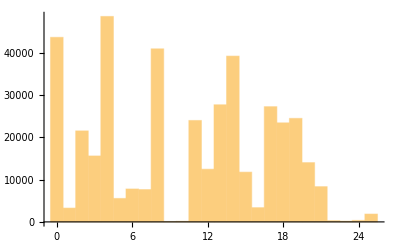

```mathematica
Histogram[divina]
```

```mathematica
messaggio
```

{0,1,1,14,13,0,19,8,12,4,13,20,2,4,17,2,0,0,1,1,14,13,0,19,8,0,1,1,14,13,0,19,8,6,4,3,8,18,12,8,11,4,12,4,13,20,3,8,13,0,21,8,6,0,25,8,14,13,4,2,14,13,19,4,13,20,19,8,15,4,17,6,11,8,0,1,1,14,13,0,19,8,6,4,3,8,18,12,18510,8,14,2,11,8,4,13,19,8,15,20,1,1,11,8,2,8,19,2,14,14,10,8,4,15,14,11,8,2,24,15,17,8,21,0,2,24,2,14,3,8,2,4,4,19,8,2,14,4,1,4,18,19,15,17,0,2,19,8,2,4,18,6,4,3,8,13,4,22,18,13,4,19,22,14,17,10,18,15,0,15,8,21,0,8,18,18,13}
 |  |  |  |

```mathematica
Count[messaggio,0]
```

2143

```mathematica
f[x_]:=Count[messaggio,x]

(Count[messaggio,#])&
```

```mathematica
Map[f,Range[0,25]]
```

{2143,244,970,941,1654,228,350,129,2612,11,43,1237,455,1392,1629,428,28,1237,857,962,516,406,26,9,25,154}

```mathematica
p=Map[(Count[divina,#])&,Range[0,25]]/Length[divina]
```

{43705/413956,818/103489,10775/206978,15615/413956,48647/413956,5553/413956,3899/206978,7655/413956,20491/206978,93/413956,145/413956,6004/103489,6237/206978,13869/206978,39259/413956,2945/103489,1685/206978,13643/206978,23457/413956,12255/206978,3509/103489,4173/206978,73/103489,171/413956,349/413956,1857/413956}

```mathematica
N[Plus@@(p^2)]
```

0.0711043